```mathematica
y[n_]:=1/n
phi[x_,n_]:=1/Pi*y[n]/(x^2+y[n]^2)
```

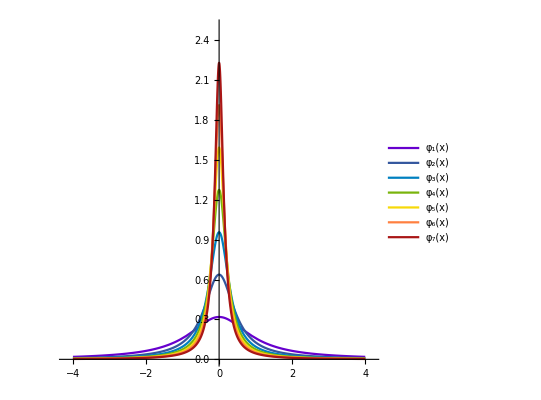

```mathematica
p =Plot[{phi[x,1],phi[x,2],phi[x,3],phi[x,4],phi[x,5],phi[x,6],phi[x,7]},{x,-4,4},PlotStyle->{RGBColor[0.403922, 0, 0.807843],RGBColor[0.203922, 0.341176, 0.619608],RGBColor[0, 0.501961, 0.752941],RGBColor[0.47451, 0.705882, 0.0470588],RGBColor[0.968627, 0.85098, 0.0352941],
RGBColor[1, 0.501961, 0.25098],RGBColor[0.662745, 0.0862745, 0.0862745]},
AspectRatio->1,
PlotRange-> {{-4.2, 4.2}, {0, 2.5}},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},LabelStyle->(FontFamily->"STIX Two Text"),
PlotLegends->{Subscript[φ,1][x],Subscript[φ,2][x],Subscript[φ,3][x],Subscript[φ,4][x],Subscript[φ,5][x],Subscript[φ,6][x],Subscript[φ,7][x]}]
```

```mathematica
Export["D:\\wolfram\\approx_2.pdf",p]
```

D:\wolfram\approx_2.pdf